```mathematica
(* Aer E 451 PS7 Problem 3 *)

ClearAll["Global`*"]
```

```mathematica
x2[t_]=x1[t]+l Sin[θ[t]];
y2[t_]=-l Cos[θ[t]];
v1[t_]=D[x1[t], t];
v2[t_]=√((D[x2[t], t])^2+(D[y2[t], t])^2);
T[t_]=1/2 m1 v1[t]^2+1/2 m2 v2[t]^2;
V[t_]=m2 g y2[t];
L[t_]=T[t]-V[t];
initconds={x1[0]==0,x1'[0]==0,θ[0]==π/9,θ'[0]==0};
ELxequ=D[D[L[t], x1'[t]], t]-D[L[t], x1[t]]==0;
ELθequ=D[D[L[t], θ'[t]], t]-D[L[t], θ[t]]==0;
```

```mathematica
tmax=5;
m1:=4
m2:=3
l:=0.1
g:=9.81
nd:=NDSolve[{ELxequ,ELθequ,initconds},{x1,θ},{t,0,tmax}]
```

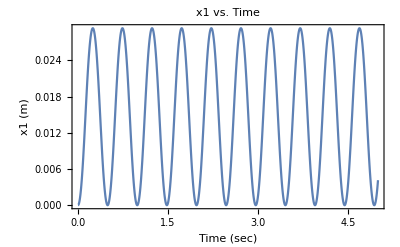

```mathematica
Plot[Evaluate[x1[t]/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","x1 (m)"},PlotLabel-> Style["x1 vs. Time",14]]
```

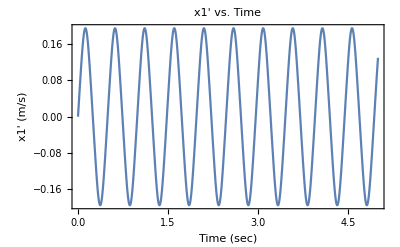

```mathematica
Plot[Evaluate[x1'[t]/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","x1' (m/s)"},PlotLabel-> Style["x1' vs. Time",14]]
```

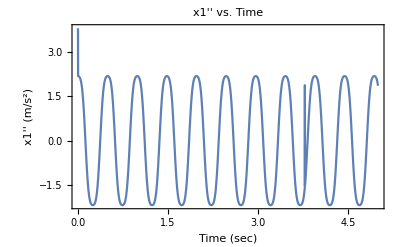

```mathematica
Plot[Evaluate[x1''[t]/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","x1'' (m/s^2)"},PlotLabel-> Style["x1'' vs. Time",14]]
```

```mathematica
(* No idea why that line appears around t = 3.8... *)
```

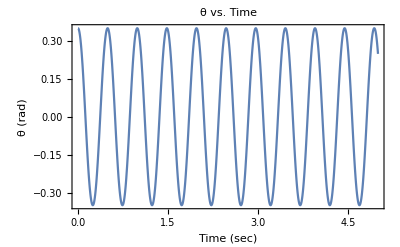

```mathematica
Plot[Evaluate[θ[t]/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","θ (rad)"},PlotLabel-> Style["θ vs. Time",14]]
```

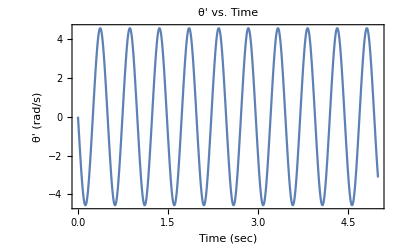

```mathematica
Plot[Evaluate[θ'[t]/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","θ' (rad/s)"},PlotLabel-> Style["θ' vs. Time",14]]
```

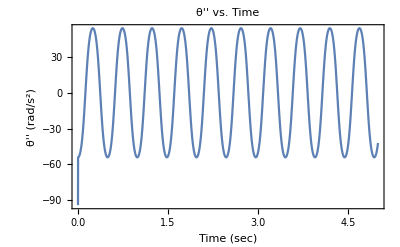

```mathematica
Plot[Evaluate[θ''[t]/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","θ'' (rad/s^2)"},PlotLabel-> Style["θ'' vs. Time",14]]
```

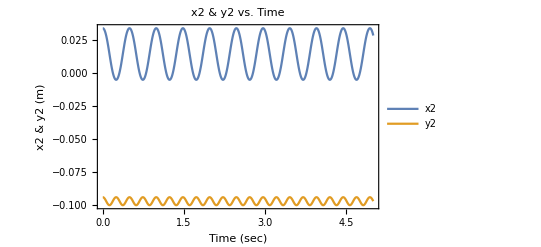

```mathematica
Plot[Evaluate[{x2[t],y2[t]}/.nd],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","x2 & y2 (m)"},PlotLabel-> Style["x2 & y2 vs. Time",14],PlotLegends->{"x2","y2"}]
```

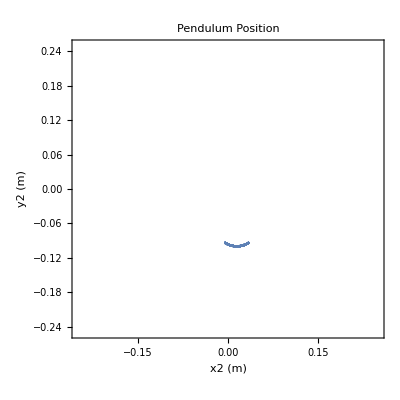

```mathematica
ParametricPlot[Evaluate[{x2[t],y2[t]}/.nd],{t,0,tmax},PlotRange->0.25,Frame->{True,True},FrameLabel->{"x2 (m)","y2 (m)"},PlotLabel-> Style["Pendulum Position",14]]
```

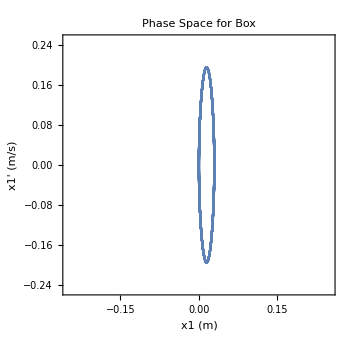

```mathematica
ParametricPlot[Evaluate[{x1[t],x1'[t]}/.nd],{t,0,tmax},PlotRange->0.25,Frame->{True,True},FrameLabel->{"x1 (m)","x1' (m/s)"},PlotLabel-> Style["Phase Space for Box",14]]
```

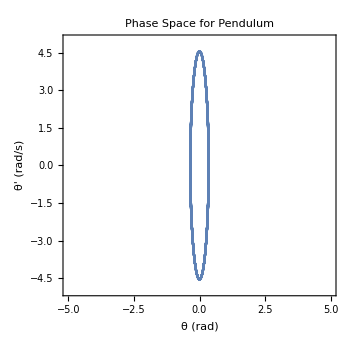

```mathematica
ParametricPlot[Evaluate[{θ[t],θ'[t]}/.nd],{t,0,tmax},PlotRange->5,Frame->{True,True},FrameLabel->{"θ (rad)","θ' (rad/s)"},PlotLabel-> Style["Phase Space for Pendulum",14]]
```